```mathematica
(* Asymmetric Cylindric Vortex Sheet *)
```

```mathematica
Phi = a/2(z^2-x^2) + b/2 (z^2-y^2) + c/2 Log[x^2 + y^2]
```

1/2 a (-x^2+z^2)+1/2 b (-y^2+z^2)+1/2 c Log[x^2+y^2]

```mathematica
Vel = Grad[Phi,{x,y,z}]
```

{-a x+(c x)/(x^2+y^2),-b y+(c y)/(x^2+y^2),a z+b z}

```mathematica
x = R[θ] Cos[θ]
```

Cos[θ] R[θ]

```mathematica
y = R[θ] Sin[θ]
```

R[θ] Sin[θ]

```mathematica
r0 = {x0,y0};
```

```mathematica
Strain0= FullSimplify[DiagonalMatrix[{-a , -b}] + Grad[Grad[Log[r0.r0],r0],r0]]
```

{{-a-(2 (x0-y0) (x0+y0))/((x0^2+y0^2)^2),-(4 x0 y0)/((x0^2+y0^2)^2)},{-(4 x0 y0)/((x0^2+y0^2)^2),-b+(2 (x0-y0) (x0+y0))/((x0^2+y0^2)^2)}}

```mathematica
Strain = Strain0/.{x0->x, y0->y}//Simplify
```

{{-a-(2 Cos[2 θ])/R[θ]^2,-(2 Sin[2 θ])/R[θ]^2},{-(2 Sin[2 θ])/R[θ]^2,-b+(2 Cos[2 θ])/R[θ]^2}}

```mathematica
(* Normal vector *)
```

```mathematica
TT0 = D[{x,y},θ]
```

{-R[θ] Sin[θ]+Cos[θ] R'[θ],Cos[θ] R[θ]+Sin[θ] R'[θ]}

```mathematica
TT2 = FullSimplify[TT0.TT0]
```

R[θ]^2+R'[θ]^2

```mathematica
TT = TT0/ Sqrt[TT2]
```

{(-R[θ] Sin[θ]+Cos[θ] R'[θ])/(√(R[θ]^2+R'[θ]^2)),(Cos[θ] R[θ]+Sin[θ] R'[θ])/(√(R[θ]^2+R'[θ]^2))}

```mathematica
NN = {TT[[2]],-TT[[1]]}
```

{(Cos[θ] R[θ]+Sin[θ] R'[θ])/(√(R[θ]^2+R'[θ]^2)),-(-R[θ] Sin[θ]+Cos[θ] R'[θ])/(√(R[θ]^2+R'[θ]^2))}

```mathematica
Snn = FullSimplify[NN.Strain.NN]
```

(-4 R[θ]^2-(a+b+(a-b) Cos[2 θ]) R[θ]^4+2 (-a+b) R[θ]^3 Sin[2 θ] R'[θ]+(4+(-a-b+(a-b) Cos[2 θ]) R[θ]^2) R'[θ]^2)/(2 R[θ]^2 (R[θ]^2+R'[θ]^2))

```mathematica
Sub = {a ->(p + q), b -> (p -q), c ->1}
```

{a→p+q,b→p-q,c→1}

```mathematica
Snn1 = Collect[ (Snn/.Sub)//TrigReduce,{R'[θ],R[θ]}]
```

(-2 R[θ]^2-p R[θ]^4-q Cos[2 θ] R[θ]^4-2 q R[θ]^3 Sin[2 θ] R'[θ]+2 R'[θ]^2-p R[θ]^2 R'[θ]^2+q Cos[2 θ] R[θ]^2 R'[θ]^2)/(R[θ]^2 (R[θ]^2+R'[θ]^2))

```mathematica
VT = (TT0.{Vel[[1]],Vel[[2]]}/.Sub)//Simplify
```

q R[θ]^2 Sin[2 θ]+R'[θ]/R[θ]-(p+q Cos[2 θ]) R[θ] R'[θ]

```mathematica
Eq =  NN.{Vel[[1]],Vel[[2]]}
```

-((-b R[θ] Sin[θ]+(c R[θ] Sin[θ])/(Cos[θ]^2 R[θ]^2+R[θ]^2 Sin[θ]^2)) (-R[θ] Sin[θ]+Cos[θ] R'[θ]))/(√(R[θ]^2+R'[θ]^2))+((-a Cos[θ] R[θ]+(c Cos[θ] R[θ])/(Cos[θ]^2 R[θ]^2+R[θ]^2 Sin[θ]^2)) (Cos[θ] R[θ]+Sin[θ] R'[θ]))/(√(R[θ]^2+R'[θ]^2))

```mathematica
Req1 = Simplify[ √(R[θ]^2+R'[θ]^2)(Eq/.Sub)//TrigReduce]
```

1-(p+q Cos[2 θ]) R[θ]^2-q R[θ] Sin[2 θ] R'[θ]

```mathematica
SnnFin=FullSimplify[Snn1/.Solve[Req1==0,R'[θ]]][[1]]
```

(2-(5 p+3 q Cos[2 θ]) R[θ]^2+2 (2 p^2-q^2+2 p q Cos[2 θ]+q^2 Cos[4 θ]) R[θ]^4-(p-q) (p+q) (p+q Cos[2 θ]) R[θ]^6)/(R[θ]^2-2 (p+q Cos[2 θ]) R[θ]^4+(p^2+q^2+2 p q Cos[2 θ]) R[θ]^6)

```mathematica
VTs = Assuming[{p >0,q >0, R[θ] >0},FullSimplify[VT/.Solve[Req1==0,R'[θ]]]][[1]]
```

(Csc[2 θ] (1-2 (p+q Cos[2 θ]) R[θ]^2+(p^2+q^2+2 p q Cos[2 θ]) R[θ]^4))/(q R[θ]^2)

```mathematica
Req2 = Req1/.{R[x_] :> Sqrt[G[x]], R'[x_] :> G'[x]/(2 Sqrt[G[x]])}
```

1-(p+q Cos[2 θ]) G[θ]-1/2 q Sin[2 θ] G'[θ]

```mathematica
Req3 = Req2/.{Cos[2 θ] ->w,G[θ] -> F[w],Sin[2 θ] G'[θ]-> -F'[w]2 (1-w^2)}
```

1-(p+q w) F[w]+q (1-w^2) F'[w]

```mathematica
Alfa[p_,q_] = (q-p)/(2 q)
```

(-p+q)/(2 q)

```mathematica
Alfa[1,-0.34]
```

1.97059

```mathematica
(*ClearAll[MyF]; 
MyF[w_,α_, q_] := 
-1/q (1 + w)^(-α) (1-w)^(α-1) Integrate[(1+ u)^(α-1) (1-u)^(-α),{u,-1,w}]*)
```

```mathematica
F0[w_,α_,q_]:= -((1-w)^(-1+α) (1+w)^-α (π Csc[π α]-Beta[(1-w)/2,1-α,α]))/q
```

```mathematica
Simplify[Req3/.{F[w] ->F0[w,Alfa[p,q] ,q], F'[w]->D[F0[w,Alfa[p,q],q],w]}]
```

0

```mathematica
FullSimplify[Beta[1,1-α,α]]
```

π Csc[π α]

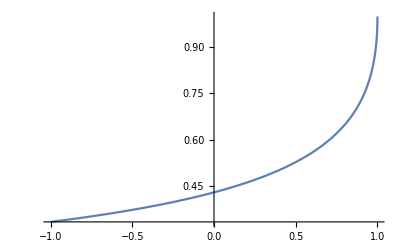

```mathematica
Plot[F0[w,Alfa[1,-0.5],-1],{w,-1,1}, PlotRange->All]
```

```mathematica
R2[θ_, p_, q_] = Sqrt[F0[w,Alfa[p,q],q]/.w ->Cos[2 θ]]
```

√(-((1-Cos[2 θ])^(-1+(-p+q)/(2 q)) (1+Cos[2 θ])^(-(-p+q)/(2 q)) (-Beta[1/2 (1-Cos[2 θ]),1-(-p+q)/(2 q),(-p+q)/(2 q)]+π Csc[(π (-p+q))/(2 q)]))/q)

```mathematica
R2[θ,1.,-0.5]
```

1.41421 √(((-3.14159-Beta[1/2 (1-Cos[2 θ]),-0.5,1.5]) (1-Cos[2 θ])^0.5)/(1+Cos[2 θ])^1.5)

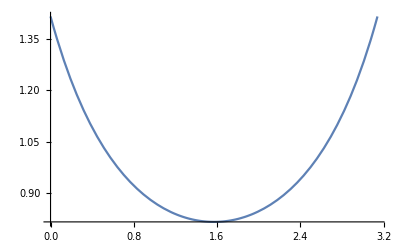

```mathematica
Plot[R2[θ,1.,-0.5],{θ,0, Pi}]
```

```mathematica
RR[θ_,p_,q_] = F0[w,Alfa[p,q],q]/.w ->Cos[2 θ]
```

-((1-Cos[2 θ])^(-1+(-p+q)/(2 q)) (1+Cos[2 θ])^(-(-p+q)/(2 q)) (-Beta[1/2 (1-Cos[2 θ]),1-(-p+q)/(2 q),(-p+q)/(2 q)]+π Csc[(π (-p+q))/(2 q)]))/q

```mathematica
SP[p_,q_] := ParametricPlot[{R2[θ,p,q] Cos[θ],R2[θ,p,q] Sin[θ]},{θ,-Pi, Pi},PlotStyle->{Red,Thick}]
```

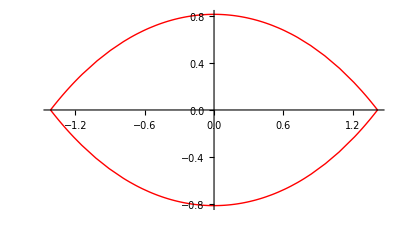

```mathematica
SP[1.,-0.5]
```

```mathematica
ClearAll[Snn1];
Snn1[θ0_,p0_,q0_] := SnnFin/.{θ->θ0,p->p0,q->q0,R[θ] :> R2[θ0,p0,q0]}
```

```mathematica
VV[θ_,p_,q_] = Simplify[(Vel.Vel)/.Sub]
```

2 p (-1+2 p z^2)-2 q Cos[2 θ]+1/R[θ]^2+(p^2+q^2+2 p q Cos[2 θ]) R[θ]^2

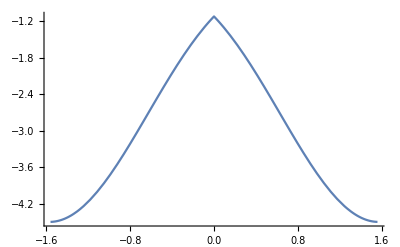

```mathematica
Plot[Snn1[θ,1.,-0.5],{θ,-Pi/2+0.01,Pi/2 -0.01}]
```

```mathematica
NMinimize[{-Snn1[θ,1.,-0.5],θ>-Pi/2,θ <Pi/2 },θ]
```

NMinimize::nnum: The function value Indeterminate is not a number at {θ} = {5.07458×10^-9}.

{0.571429,{θ→7.73369×10^-9}}

```mathematica
NMinimize[{Snn1[θ,1.,-0.33],θ>-Pi/2,θ <Pi/2 },θ]
```

{-3.98972,{θ→-1.55971}}

```mathematica
SS[p_,q_] := ParametricPlot[{Sqrt[-Snn1[θ,p,q]] Cos[θ],Sqrt[-Snn1[θ,p,q]] Sin[θ]},{θ,-Pi, Pi}]
```

```mathematica
SS[1.,-0.5];
```

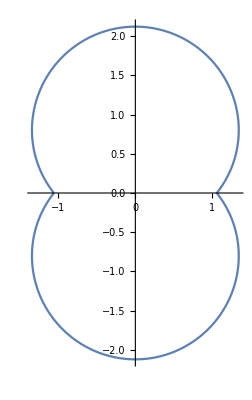

-Graphics-

```mathematica
SolR = Solve[Req1==0,R'[θ]][[1,1]]
```

R'[θ]→-(Csc[2 θ] (-1+p R[θ]^2+q Cos[2 θ] R[θ]^2))/(q R[θ])

```mathematica
Simplify[TT2/.SolR]
```

R[θ]^2+(Csc[2 θ]^2 (-1+(p+q Cos[2 θ]) R[θ]^2)^2)/(q^2 R[θ]^2)

```mathematica
ClearAll[TT0];TT0[θ_,p_,q_] = Simplify[TT2/.SolR]/.R[θ]->R2[θ,p,q];
```

```mathematica
EE[p_,q_] := 4/3 p^2 NIntegrate[With[{F0 =TT0[θ,p,q], T0 =-Snn1[θ,p,q]},  F0 Sqrt[T0] ],{θ,+0.0001 , Pi/2-0.0001 }]
```

```mathematica
EE[1.,-0.5]
```

3.98599

```mathematica
3.6428659119922266
```

3.64287

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.56876050925536565596070393002747778155026026070117950439453125}. NIntegrate obtained -129655.+1332.66 ⅈ and 40814. for the integral and error estimates.

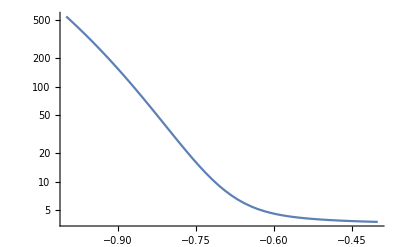

```mathematica
LogPlot[EE[1.,q],{q,-1.,-0.4},PlotRange->All]
```

```mathematica
VT0[θ_,p_,q_] = VTs/.R[θ]-> R2[θ,p,q]
```

-(((1-Cos[2 θ])^(1-(-p+q)/(2 q)) (1+Cos[2 θ])^((-p+q)/(2 q)) (1+(2 (1-Cos[2 θ])^(-1+(-p+q)/(2 q)) (1+Cos[2 θ])^(-(-p+q)/(2 q)) (p+q Cos[2 θ]) (-Beta[1/2 (1-Cos[2 θ]),1-(-p+q)/(2 q),(-p+q)/(2 q)]+π Csc[(π (-p+q))/(2 q)]))/q+1/q^2(1-Cos[2 θ])^(-2+(-p+q)/q) (1+Cos[2 θ])^(-(-p+q)/q) (p^2+q^2+2 p q Cos[2 θ]) (-Beta[1/2 (1-Cos[2 θ]),1-(-p+q)/(2 q),(-p+q)/(2 q)]+π Csc[(π (-p+q))/(2 q)])^2) Csc[2 θ])/(-Beta[1/2 (1-Cos[2 θ]),1-(-p+q)/(2 q),(-p+q)/(2 q)]+π Csc[(π (-p+q))/(2 q)]))

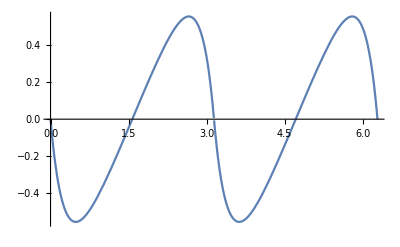

```mathematica
Plot[VT0[θ,1.,-0.5],{θ,0,2Pi}]
```

```mathematica
VL0[θ_,p_, q_] =  VT0[θ,p,q]/TT0[θ,p,q];
```

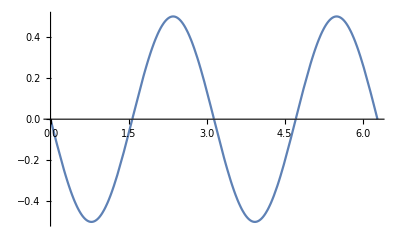

```mathematica
Plot[VL0[θ,1.,-0.5],{θ,0,2Pi}]
```

```mathematica
Vel2[a_,b_, u_,v_]:= {- a u  + u/(u^2 + v^2), - b v + v/(u^2 + v^2)}
```

```mathematica
Flow[p_,q_]:=Show[{
StreamPlot[
If[(u^2+v^2)>RR[ArcTan[u,v],p,q],
Vel2[p+q,p-q,u,v],
{0,0}
],{u,-2,2},{v,-2,2},
StreamColorFunction->"DarkRainbow"
],
SP[p,q]
}]
```

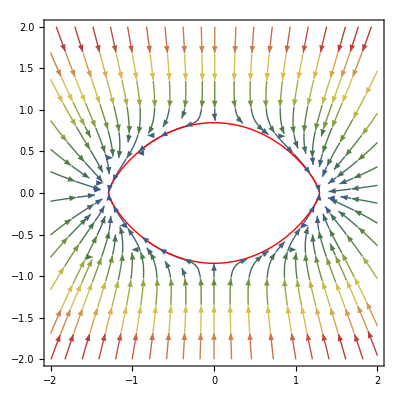

```mathematica
Flow[1.0,-0.4]
```

```mathematica
Flow[1.0,-0.5]
```

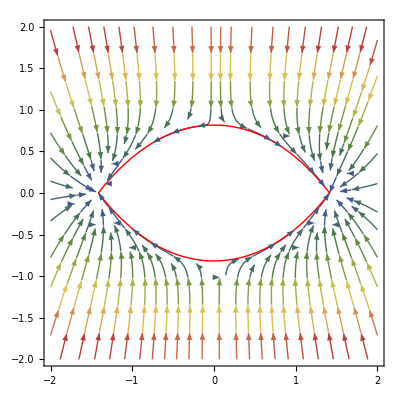

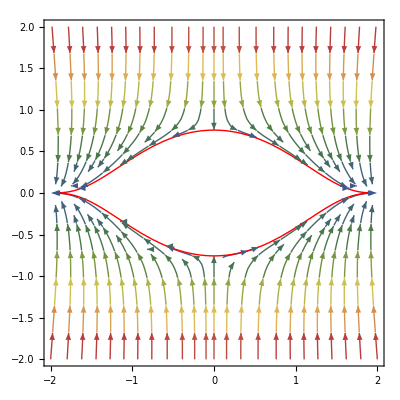

```mathematica
Flow[1.0,-0.75]
```

```mathematica
4 Pi 24840/(5*2304 Pi^2)
```

69/(8 π)

```mathematica
R2[θ,p,q]
```

√(-((1-Cos[2 θ])^(-1+(-p+q)/(2 q)) (1+Cos[2 θ])^(-(-p+q)/(2 q)) (-Beta[1/2 (1-Cos[2 θ]),1-(-p+q)/(2 q),(-p+q)/(2 q)]+π Csc[(π (-p+q))/(2 q)]))/q)

```mathematica
TT0[θ,p,q]
```

-((1-Cos[2 θ])^(-1+(-p+q)/(2 q)) (1+Cos[2 θ])^(-(-p+q)/(2 q)) (-Beta[1/2 (1-Cos[2 θ]),1-(-p+q)/(2 q),(-p+q)/(2 q)]+π Csc[(π (-p+q))/(2 q)]))/q-((1-Cos[2 θ])^(1-(-p+q)/(2 q)) (1+Cos[2 θ])^((-p+q)/(2 q)) (-1-((1-Cos[2 θ])^(-1+(-p+q)/(2 q)) (1+Cos[2 θ])^(-(-p+q)/(2 q)) (p+q Cos[2 θ]) (-Beta[1/2 (1-Cos[2 θ]),1-(-p+q)/(2 q),(-p+q)/(2 q)]+π Csc[(π (-p+q))/(2 q)]))/q)^2 Csc[2 θ]^2)/(q (-Beta[1/2 (1-Cos[2 θ]),1-(-p+q)/(2 q),(-p+q)/(2 q)]+π Csc[(π (-p+q))/(2 q)]))

```mathematica
AA[p_,q_] := 4NIntegrate[TT0[θ,p,q]R2[θ,p,q],{θ,+0.0001 , Pi/2-0.0001 }]
```

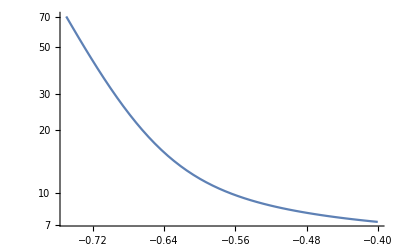

```mathematica
LogPlot[AA[1,q],{q,-0.75,-0.4}]
```